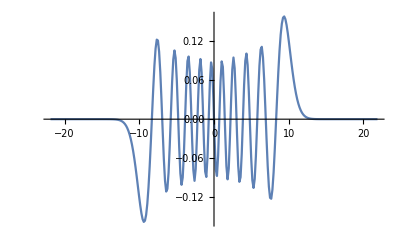

```mathematica
V[s_] := Abs[s]; ϵm = 20.;
st = FindRoot[V[s]==ϵm,{s,ϵm}] ⟦1,2⟧; 
ds = 1/ Sqrt[2 ϵm];
n = Round[2 (st/ds+ 4  Pi)];
s= Table [-ds*(n+1)/2 + ds*i, {i,n}];
one[n_,d_] :=
 DiagonalMatrix[1+ 0 Range[n-Abs[d]],d];
B = (one[n,-1]+ 10 one[n,0] +one[n,1])/12.;
A = (one[n,-1]- 2 one[n,0] +one[n,1])/ds^2;
KE = -Inverse[B].A/2;
H= KE+ DiagonalMatrix[V[s]];
{eval, evec} = Eigensystem[H];
ListPlot[Transpose[{s,evec[[-20]]}], Joined -> True]

evec;
```